{π/3,0}

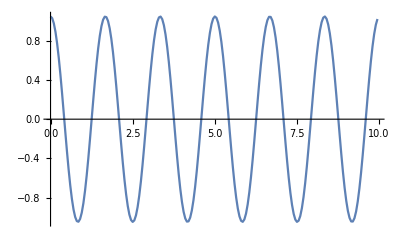

```mathematica
(*Runge Kutta mothod of order 4*)
RK[f_, t_, x_, h_, n_] :=
(*adding N[,30] makes our calculation more precise. But we need to take out 1. in places*)
Module[{i, s=t, k1, k2, k3, k4, y=x, h2=N[h/2,30]},
For[i=1, i≤n, i++,
k1=h*f[s, y];
s=s+h2;
k2=h*f[s, y+k1/2];
k3=h*f[s, y+k2/2];
s=s+h2;
k4=h*f[s, y+k3];
y=y+(k1+2 k2+2 k3+k4)/6];
y];

g[t_, x_] :={ x[[2]],-(9.8/.6)*Sin[x[[1]]]};

(*used for example 1 in notes*)
tf=.1;
(*n=100;*)
(*used for example 2 in notes*)
a=Pi/3;
dt=.05; (*if we make larger steps then we will see the plot has kinks, not smooth*)
n=10;
x={a, 0}

(*we have solved problems with RK Order 4 before but here we first converted higher order derivatives so we could work with them*)
(*example 1 in notes*)
(*RK[g, 0., {1.,0.}, tf/n, n] -{Cos[tf], -Sin[tf]}(*subtract for error*)*)

(*example 2 in notes - pendulum*)
 (*RK[g, 0., {0,a}, tf/n, n]*)

(*we will make a list of data so we can plot*)
(*a lot of solvers work like this by making a list then we can interpolate on this say with splines*)
lst={};
For[t=0., t<10,t=t+dt,
lst=Append[lst,{t,x[[1]]}];
x=RK[g, t, x, dt/n, n]];

ListPlot[lst, Joined->True]
```

```mathematica
t=.35;
For[i=0,i<10,i++,
x=RK[g,0,{0.,a},t/n,n];
t=t+ x[[2]]/((9.8/.6)*Sin[x[[1]]]);
Print[4t,"  ", x[[2]]]]
```

1.56267  0.168477

1.56128  -0.00145961

1.56128  -3.52797×10^-8

1.56128  -8.7344×10^-13

1.56128  -2.22045×10^-16

1.56128  1.11022×10^-16

1.56128  1.11022×10^-16

1.56128  1.11022×10^-16

«2 more identical outputs»